```mathematica
language = "Croatian"
```

Croatian

```mathematica
alfabet = Alphabet[language]
```

{a,b,c,č,ć,d,dž,đ,e,f,g,h,i,j,k,l,lj,m,n,nj,o,p,r,s,š,t,u,v,z,ž}

```mathematica
dl = Length[alfabet]
```

30

```mathematica
pary = Tuples[alfabet,2]
```

{{a,a},{a,b},{a,c},{a,č},{a,ć},{a,d},{a,dž},{a,đ},{a,e},{a,f},{a,g},{a,h},{a,i},874,{ž,m},{ž,n},{ž,nj},{ž,o},{ž,p},{ž,r},{ž,s},{ž,š},{ž,t},{ž,u},{ž,v},{ž,z},{ž,ž}}
 |  |  |  |

```mathematica
zlaczone = Table[StringJoin[pary[[i]]],{i,1,Length[pary]}];
```

```mathematica
liczby = Table[Length[DictionaryLookup[{language, zlaczone[[i]]~~__}] ],{i,1,Length[pary]}];
```

```mathematica
a = GatherBy[pary, First] ;
```

```mathematica
wartosci =Table[Table[Length[DictionaryLookup[{language,StringJoin[a[[j]][[i]]]~~__}]],{i,1,Length[alfabet]}],{j,1,Length[alfabet]}];
```

```mathematica
epilog = Table[Text[liczby[[i]],{dl - ((dl-Flatten[Position[alfabet,pary[[i]][[2]]]][[1]])+1/2),
dl - ((dl-(dl-Flatten[Position[alfabet,pary[[i]][[1]]]][[1]]))-1/2)}],{i,1,Length[pary]}];
```

```mathematica
osie = Table[{i,alfabet[[i]]},{i,1,dl}];
podpisyOsi = Style[#, 16, Black] & /@ {"Druga litera", "Pierwsza litera"}
```

{Druga litera,Pierwsza litera}

```mathematica
Jeden = MatrixPlot[wartosci,Epilog->epilog,ImageSize->1000,ColorRules->{0->White},ColorFunction->(ColorData[{"LakeColors","Reverse"}]),FrameTicks ->{osie,osie,osie,osie},FrameTicksStyle->{{14,Black},{14,Black},{14,Black},{14,Black}},   FrameLabel -> Transpose[{podpisyOsi, podpisyOsi}],  PlotLegends -> 
    Placed[Style["Liczba słów w języku chorwackim", 20, Black, Bold], Above]]
```

-Graphics-

```mathematica
cloud = Table[{zlaczone[[i]],liczby[[i]]},{i,1,Length[liczby]}]
```

{{aa,0},{ab,136},{ac,15},{ač,0},{ać,0},{ad,255},{adž,0},{ađ,0},{ae,58},{af,150},{ag,246},{ah,0},{ai,1},{aj,11},872,{žlj,0},{žm,0},{žn,0},{žnj,0},{žo,0},{žp,0},{žr,0},{žs,0},{žš,0},{žt,0},{žu,0},{žv,0},{žz,0},{žž,0}}
 |  |  |  |

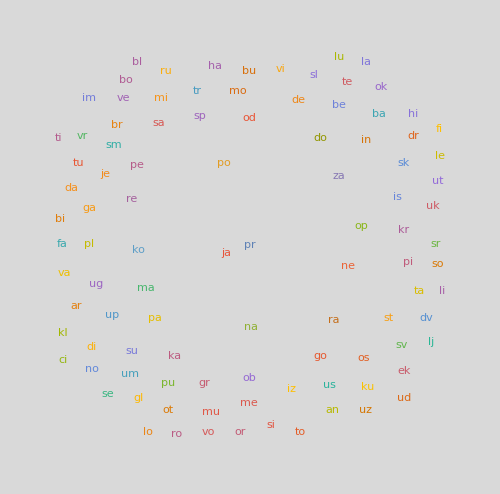

```mathematica
Dwa = WordCloud[cloud,Background->LightGray,ImageSize->500]
```

```mathematica
GraphicsRow[{Jeden,Dwa},Frame->All,ImageSize->{2200,1500}]
```

-Graphics-

```mathematica
CloudExport[%,"pdf"]
```

CloudObject[https://www.wolframcloud.com/obj/fc785d43-368a-4a77-9ead-ef6c31bf4939]